### Adaptively evolving hypergraphs

### Tracing line from null rule to doubling program

```mathematica
ads =Take[ResourceData["Three-Color Cellular Automaton Rules that Double Their Input"],All];
```

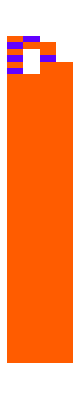
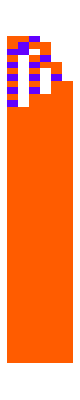
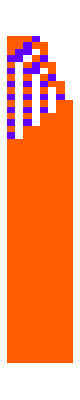
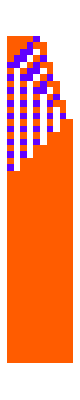
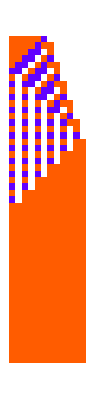
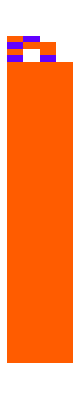
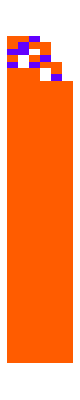
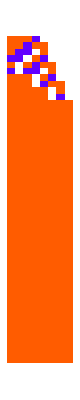
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[ArrayPlot[CellularAutomaton[{#, 3, 1}, {Append[Table[1, i], 2], 0}, 50]], {i, 5}]&/@
```

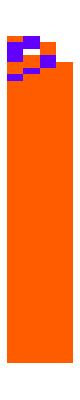
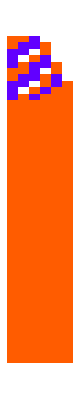
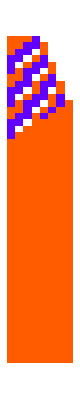
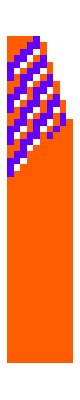
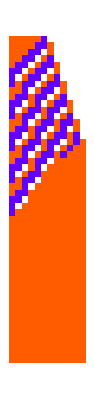
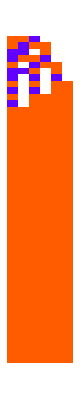
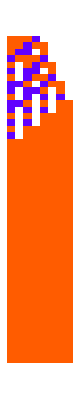
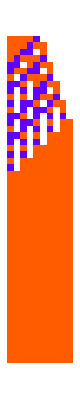
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
SeedRandom[333225];Table[ArrayPlot[CellularAutomaton[{#, 3, 1}, {Append[Table[1, i], 2], 0}, 50]], {i, 5}]&/@RandomSample[ ads, 10]
```

```mathematica
RuleSequencePlot[{#, 3, 1}]&/@
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Length[ads]
```

199

#### Rule sequence frequency

```mathematica
Column[MapThread[Function[{digs,label},With[{aps=Rasterize[ArrayPlot[List/@#,ImageSize->{10,25},ColorRules->colorrules]]&/@RuleTuples[3,1]},BarChart[BinCounts[#,{0,4,1}]&/@Transpose[digs],ChartLayout->"Stacked",ChartBaseStyle->EdgeForm[Thickness[.1]],ChartStyle->(Directive[EdgeForm[Directive[Opacity[1],Gray]],#]&)/@{{"[◼]", "CustomStyleData"}}["Colors"][[All,2]],ChartLabels->{aps,None},LabelingSize->35,AspectRatio->.4,ImageSize->{600,Automatic},Frame->True,FrameLabel->{"rule","counts"},PlotLabel->label]]],{{(Append[#,0]&/@RandomChoice[{0,1,2},{200,3^(2*1+1)-1}]),Module[{digits,n,k,r},{n,k,r}=#;
digits=IntegerDigits[n,k,k^(2r+1)]]&/@({#, 3, 1}&/@ ads)},{"Random","Evolved"}}]]
```

-Graphics-
-Graphics-

```mathematica
ArrayPlot[ArrayFlatten[IntegerDigits[#, 3, 27]&/@ ads]]
```

-Graphics-

#### Showing possible evolution paths

Different rules

```mathematica
SeedRandom[3323];
NestWhileList[
Module[{digs}, 
digs = IntegerDigits[#, 3, 27];
colidxs = Flatten[Position[digs, x_/;x>0]];
FromDigits[MapAt[0&,digs,RandomChoice[colidxs]], 3]]&,#, # !=0&]&/@ RandomSample[ads, 10]
```

{{7052074227936,7031153521530,5336576302644,5336576302617,5336575948323,5336188527834,5336188514712,5335026253245,5335026194196,5334940100754,5334938506431,5146652148777,5146652148696,5146652148210,5146523008047,62791351389,62790819948,62790817761,28698543,28697814,0},{6463950373854,6443029667448,6443029666719,6443029666233,6411648606624,6411647012301,6411646480860,6411517340697,6411517340616,6411129920127,6128700383646,6128700383619,6121726814817,6121640721375,6121640719188,6121631153250,6121631146689,5933344789035,5086056179592,5083731656658,0},{7050878133579,6988116014361,6988106448423,6988077750609,6987948610446,6987561189957,6987561185583,6966640479177,6966640478448,6966640478367,5272063259481,5272063259454,5272020212733,5272018618410,5083732260756,5083731729315,5083731670266,13608,13122,0},{532801203786,530476680852,530476680366,530475086043,530474908896,530474908167,530465342229,509544635823,509544104382,227114567901,195733508292,195733506105,195733506024,195647412582,195647353533,188673784731,188673778170,387420516,27,0},{4541584617225,4541197196736,4541196665295,4541196663108,4541067522945,1999201694616,1999201681494,1999201681008,1999200086685,1999190520747,1999176171840,1999176171759,1999176171030,1999090077588,1999089723294,1997927461827,303350242941,282429536535,282429536481,0},{7051896846927,7051896315486,5357319096600,5357276049879,5357276049150,5336355342744,5336345776806,5148059419152,5147671998663,5147671998582,5147657649675,5084895530457,5084895517335,5084893923012,5084893922985,5084893918611,5083731657144,486,0},{5922408276981,5922407745540,5922407745054,5922149464728,5922149464674,5357290391712,5357261693898,5357261687337,5336340980931,252609324273,189847205055,189847204974,189845610651,189836044713,189836043984,189448623495,1162265841,1162261467,0},{3074666854968,3053746148562,511880320233,511870754295,323584396641,323584337592,323498244150,323498244123,292117184514,292117183785,292117181598,292117181517,285143612715,282819089781,282819083220,282817488897,387952416,387951930,387420489,0},{50749611912,49587350445,49587350391,49587350310,49199929821,49199929335,49199752188,48941471862,48912774048,48826680606,48826149165,41852580363,10471520754,10471520025,10471513464,10461947526,10460353203,0},{6735962722464,6735575301975,6735574770534,6735574770480,6735574770237,5888286160794,5856905101185,5856895535247,5856895535166,5856895528605,5292036455643,5292036454185,5292036336087,208304679429,205980156495,17693798841,10720230039,10461949713,10460355390,2187,0}}

```mathematica
GraphicsRow/@(ArrayPlot[CellularAutomaton[{#, 3, 1}, {Append[Table[1, 5], 2], 0}, 50]] &/@ #&/@ )
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Same rule multiple paths

```mathematica
NestWhileList[
Module[{digs}, 
digs = IntegerDigits[#, 3, 27];
colidxs = Flatten[Position[digs, x_/;x>0]];
FromDigits[MapAt[0&,digs,RandomChoice[colidxs]], 3]]&,#, # !=0&]&/@ Table[ads[[2]], 20];
```

```mathematica
GraphicsRow/@(ArrayPlot[CellularAutomaton[{#, 3, 1}, {Append[Table[1, 5], 2], 0}, 50]] &/@ #&/@ [[;;10]])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphicsRow/@(ArrayPlot[CellularAutomaton[{#, 3, 1}, {Append[Table[1, 5], 2], 0}, 50]] &/@ #&/@ [[;;19]])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}